## Basic Epidemic Model

0.0028

0.44

s'[t]==-0.0028 i[t] s[t]

i'[t]==-0.44 i[t]+0.0028 i[t] s[t]

{{s[t]→InterpolatingFunction[…][t],i[t]→InterpolatingFunction[…][t]}}

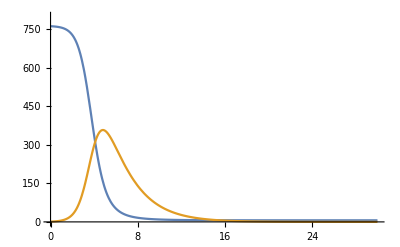

```mathematica
Clear[s,t,i,sol]
beta = 2.8*10^-3
gamma = 0.44
de1 = s'[t]==-beta*s[t]*i[t]
de2 = i'[t]==beta*s[t]*i[t]-gamma*i[t]
sol=NDSolve[{de1,de2,s[0]==762,i[0]==1},{s[t],i[t]},{t,0,30}]
Plot[Evaluate[{s[t],i[t]}/.sol],{t,0,30},PlotRange->{0,800}]
```

1/1000000

1000000

1/50

1/3

s'[t]==20000-s[t]/50-(i[t] s[t])/1000000

i'[t]==-(53 i[t])/150+(i[t] s[t])/1000000

{{s[t]→InterpolatingFunction[…][t],i[t]→InterpolatingFunction[…][t]}}

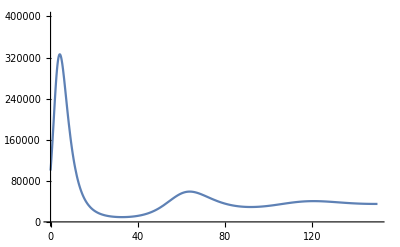

```mathematica
Clear[s,t,i,sol,beta,gamma,de1,de2]
beta = 10^-6
n=10^6
a=b=1/50
gamma = 1/3
de1 = s'[t]==b*n-beta*s[t]*i[t]-a*s[t]
de2 = i'[t]==beta*s[t]*i[t]-gamma*i[t] -a*i[t]
sol=NDSolve[{de1,de2,s[0]==9*10^5,i[0]==10^5},{s[t],i[t]},{t,0,150}]
Plot[Evaluate[{i[t]}/.sol],{t,0,150},PlotRange->{0,4*10^5}]
```